# D2: Orthogonality

The gold-standard most stable linear algebra computations are based on operations with orthogonal matrices.  We need to be able to build rotations (and associated projectors) to do useful tasks.

## Projectors and Orthogonality

### Calculus II

In Calculus II you defined projectors onto a vector u as an operator (clearly linear although you may not have bothered saying it) as 
	v→(<v,u>)/(<u,u>)u=(v.u)/(u.u)u
You immediately realized that this was cleaner if u was normalized! The simpler formula for the projector onto a unit (||u||=1) vector 
	v→(v.u)u
and the complementary projection onto u^⊥
	v→v-(v.u)u
hopefully look familiar! Since these are linear operators they have matrices!

We want to know how to tell if a matrix is a projection.

We want to know how to efficiently build useful projection matrices.

### Linear Algebra: Eigenstuff

In linear algebra you learned eigenvalue-eigenvector pairs of A satisfy
	A.v=λ v.
You did not learn how to compute them for large matrices!

You did learn that for real symmetric m×m matrices A=Aᵀ:

The m eigenvalues λ_k were real.

The m eigenvectors v_k could be chosen real and orthogonal!

### Projector: Definitions etc.

An m×m matrix P is a projector if P^2=P.P=P.  The fancy word for this property is “Idempotent”. It simply says multiplying by P once is the same as doing it more than once!

For a projector P the complementary projector is I-P

An orthogonal projector has P=P^*

Eigenvalues of P are all either 1 or 0.

### Householder Reflector

The Householder Reflector associated with an orthogonal projector P is the Orthogonal matrix Q=I-2P.

### Tall Skinny A: Orthogonal Projector onto Column Space of A

If A is full rank then the orthogonal projector onto the column space of A is P=A.(A^*.A)^-1.A^*

### Tall Skinny Q: Orthogonal Projector onto Orthogonal basis

If a Tall-Skinny m×n matrix Q has orthogonal columns then Q^*.Q=I_n! and the orthogonal projector is P=Q.Q^*.

This has limited utility until we know how compute an orthogonal Q

### Computations

Checking some stuff.

```mathematica
{m,n}={17,4};
A=RandomReal[{-1,1},{m,n}];
P=A.Inverse[Aᵀ.A].Aᵀ;
H=IdentityMatrix[m]-2P;
{Dimensions[P],Map[Norm,{P-P.P,P-Pᵀ,H.Hᵀ-IdentityMatrix[m]}]}
MatrixPlot[P];
```

{{17,17},{5.26644×10^-16,1.54276×10^-16,1.87372×10^-15}}

```mathematica
{m,n}={17,4};
A=RandomReal[{-1,1},{m,n}];
P=A.Inverse[Aᵀ.A].Aᵀ; H=IdentityMatrix[m]-2P;
Map[Eigenvalues,{P,H}]
```

{{1.,1.,1.,1.,1.33193×10^-16,1.06953×10^-16,-5.00208×10^-17,-3.7004×10^-17,-3.12952×10^-17,-3.12952×10^-17,2.87129×10^-17,2.87129×10^-17,2.35099×10^-17,-2.05178×10^-17,1.31047×10^-17,1.01489×10^-17,1.01489×10^-17},{1.,-1.,-1.,1.,1.,-1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,-1.,1.}}

## QRDecomposition

### Matrices with orthogonal columns are useful!

Our target is to construct an orthogonal basis for the column space of a Tall-Skinny m×n matrix
	A=[a_1|a_2|…|a_n].
This basis is naturally represented by a Tall-Skinny m×n matrix
	Q=[q_1|q_2|…|q_n].
We will learn how to compute a QR decomposition A=Q.R where the new matrix R (which tells us how to combine the columns of A to compute Q) is upper triangular!

Every software package has a QR decomposition.  Different packages return the bits in different ways! Always read the documentation and check! Mathematica returns Q on its side!

{1.67431×10^-15,6.85911×10^-16}

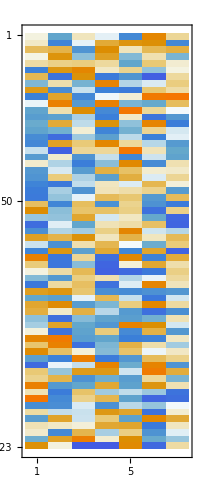
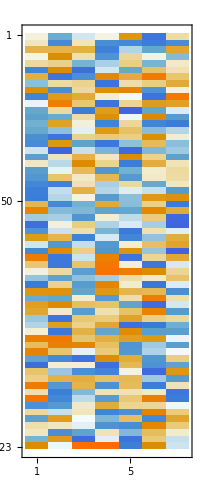
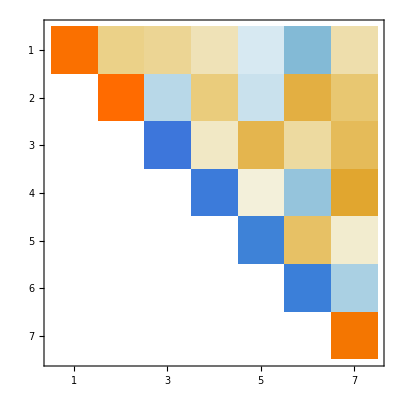

```mathematica
{m,n}={123,7};
A=RandomReal[{-1,1},{m,n}]; 
{Q,R}=QRDecomposition[A];
(* Mathematica #$#@$ returns Q on it side *)
Q=Qᵀ;
Map[Norm,{A-Q.R,Qᵀ.Q-IdentityMatrix[n]}]
Map[MatrixPlot,{A,Q,R}]
```

We are going to learn one way the computer could do this.  Well actually we are going to learn a bunch but the first one is called the Gram-Schmidt process.

### Gram-Schmidt: Idea

The motto here is start at the very beginning of
	A=[a_1|a_2|…|a_n]
and work through the columns!

First, normalize the first column by dividing by ||a_1|| and define
	q_1=a_1/(||a_1||).

Next, project out the component of a_2 in the direction of q_1
	q_2=a_2-(a_2.q_1)q_1
and normalize
	q_2=q_2/||q_2||.
Note we have recycled q_2 repeatedly to accumulate the correct expression.

The next step is more of the same but we need to get a bit more organized!  Pick the next column
	w=a_3
project out the components in q_1 and q_2
	w | = | w-(w.q_1)q_1
w | = | w-(w.q_2)q_2
and normalize
	q_3=w/||w||.
I am using w as mnemonic for work vector!

The next step is more of the same but we need to get a bit more organized!  Pick the next column
	w=a_4
project out the components in q_1 and q_2
	w | = | w-(w.q_1)q_1
w | = | w-(w.q_2)q_2
w | = | w-(w.q_3)q_3
and normalize
	q_4=w/||w||.

All we have to do is keep going until we run out of columns!  We are left with the tall-skinny matrix Q.  The only problem is we do not have the recipe for how we combined the columns: it is all stored in the inner products and scalings of the vectors.

### Gram-Schmidt: Manual

Here is a hand walk through of for a three column matrix! I am saving the coefficients so that we can see where they go!

```mathematica
{m,n}={5,3};
A=RandomReal[{-1,1},{m,n}];
(* First column *)
 v=A⟦All,1⟧;
c1=Norm[v];
q1 =v/c1;
(* second column *)
v=A⟦All,2⟧;
c21 =v.q1;
v=v-c21 q1;
c2=Norm[v];
q2 =v/c2;
(* Third column *)
v=A⟦All,3⟧;
c31 =v.q1;
v=v-c31 q1;
c32 =v.q2;
v=v-c32 q2;
c3=Norm[v];
q3 =v/c3;
MyQ={q1,q2,q3};
{c1,{c21,c2},{c31,c32,c3}}
```

{1.17406,{0.49415,1.50024},{0.030339,-0.549153,0.530774}}

Lets compare to the built-in QR

```mathematica
{BuiltInQ,BuiltInR}=QRDecomposition[A];
BuiltInR
```

{{-1.17406,-0.49415,-0.030339},{0.,1.50024,-0.549153},{0.,0.,-0.530774}}

Our numbers match (except for the signs) and I think we can work out how to construct R

### Gram-Schmidt: Script

Here is a preliminary script!

{5.58978×10^-16,2.49574×10^-15}

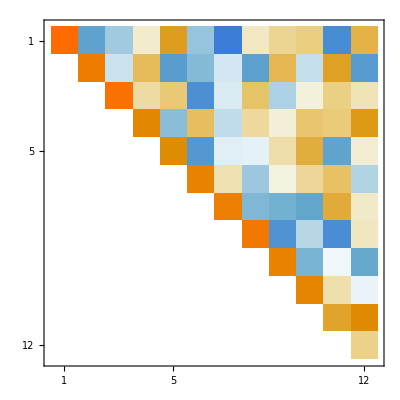

```mathematica
{m,n}={14,12};
A=RandomReal[{-1,1},{m,n}];
(* Set up Storage *)
Q=0*A; R=ConstantArray[0,{n,n}];
(* Loop through columns *)
Do[
(* Grab next column *)
v=A⟦All,j⟧;
(* project out previous columns *)
Do[
R⟦i,j⟧=v.Q⟦All,i⟧;
v=v-R⟦i,j⟧ Q⟦All,i⟧,
{i,1,j-1}];
(* Scale and save orthogonalized columns *)
R⟦j,j⟧=Norm[v];
Q⟦All,j⟧=v/R⟦j,j⟧;,
{j,1,n}]
(* Check that we computed a QR Decomposition *)
Map[Norm,{A-Q.R,Qᵀ.Q-IdentityMatrix[n]}]
(*{OrthogonalMatrixQ[Q],UpperTriangularMatrixQ[R]}*)
MatrixPlot[R]
```

### Gram-Schmidt: Function

Here is a function to hide all the crud!

```mathematica
MyGramSchmidt[A_]:= Module[{m,n,Q,R,v},
{m,n}=Dimensions[A];
(* Set up Storage *)
Q=0*A; R=ConstantArray[0,{n,n}];
(* Loop through columns *)
Do[
(* Grab next column *)
v=A⟦All,j⟧;
(* project out previous columns *)
Do[
R⟦i,j⟧=v.Q⟦All,i⟧;
v=v-R⟦i,j⟧ Q⟦All,i⟧,
{i,1,j-1}];
(* Scale and save orthogonalized columns *)
R⟦j,j⟧=Norm[v];
Q⟦All,j⟧=v/R⟦j,j⟧,
{j,1,n}];
{Q,R}]
```

Here is a test

```mathematica
{m,n}={700,450};
A=RandomReal[{-1,1},{m,n}];
AbsoluteTiming[{Q,R}=MyGramSchmidt[A];]
AbsoluteTiming[{Q2,R2}=QRDecomposition[A];]
AbsoluteTiming[Z=Q2ᵀ;]
(* Check that we computed a QR Decomposition *)
Map[Norm,{A-Q.R,Qᵀ.Q-IdentityMatrix[n]}]
UpperTriangularMatrixQ[R]
```

{2.22633,Null}

{0.017821,Null}

{0.0009307,Null}

{2.0176×10^-14,2.04765×10^-15}

True

### Efficiency: Math Libraries

The built in QR decomposition is going to be MUCH faster than any code we write. The reason is that the basic QR computation is the foundation for a lot of other fancier computations.  As a result, a substantial effort has been made to make it as efficient as possible.  This includes economizing storage and computation and communication.

All the higher level tools rely on libraries of math functions.  The lowest level is called BLAS for Basic Linear Algebra Subprograms which are designed to squeeze every possible bit of performance out of all sorts of hardware.

One of the reasons Julia is fast (the Julia folks use the word performant) and one of the reasons we are going to look at Julia is that it makes it easy to access these libraries. Good code uses these libraries!

```mathematica
{m,n}={1500,111};
A=RandomReal[{-1,1},{m,n}];
Timing[{Q,R}=MyGramSchmidt[A];]
Timing[{Q,R}=QRDecomposition[A];]
```

{0.515625,Null}

{0.015625,Null}

### Math Libraries

Math libraries (BLAS, MKL, ...) are portable, fast, and an all round good idea!

We are about to see that subtle algorithmic differences can significantly impact stability and performance!

Real QR codes would never do GS (7.1) when MGS (8.1) is better and almost the same amount of work. Both treat R as the main product and Q as a byproduct.

Most of the time Q is the thing folks want and R is just thrown away. In this case the Householder algorithm we are going to talk about later which targets Q gives more orthogonal matrices.

### Modified Gram-Schmidt

Here is our implementation of GS 7.1

```mathematica
MyGramSchmidt[A_]:= Module[{m,n,Q,R,v},
{m,n}=Dimensions[A];
(* Set up Storage *)
Q=0*A; R=ConstantArray[0,{n,n}];
(* Loop through columns *)
Do[
(* Grab next column *)
v=A⟦All,j⟧;
(* project out previous columns *)
Do[
R⟦i,j⟧=Q⟦All,i⟧.A⟦All,j⟧;
v=v-R⟦i,j⟧ Q⟦All,i⟧,
{i,1,j-1}];
(* Scale and save orthogonalized columns *)
R⟦j,j⟧=Norm[v];
Q⟦All,j⟧=v/R⟦j,j⟧;,
{j,1,n}];
{Q,R}]
```

Here is an implementation of Modified GS 8.1

```mathematica
MyModifiedGramSchmidt[A_]:= Module[{m,n,Q,R,V},
{m,n}=Dimensions[A];
V=A;Q=0*A; R=ConstantArray[0,{n,n}];
Do[
R⟦i,i⟧=Norm[V⟦All,i⟧];
Q⟦All,i⟧=V⟦All,i⟧/R⟦i,i⟧;
Do[
R⟦i,j⟧=Q⟦All,i⟧.V⟦All,j⟧;
V⟦All,j⟧=V⟦All,j⟧-R⟦i,j⟧ Q⟦All,i⟧,
{j,i+1,n}],
{i,1,n}];
{Q,R}]
```

Testing and comparing the two versions! Both work.

```mathematica
{m,n}={400,399};
A=RandomReal[{-1,1},{m,n}];
TableForm[
Table[
time=AbsoluteTiming[{Q,R}=qr[A];]⟦1⟧;{qr,time,Norm[Qᵀ.Q-IdentityMatrix[n]],Norm[A-Q.R]},
{ qr,{MyGramSchmidt,MyModifiedGramSchmidt}}],
TableHeadings->{None,{"Algorithm","Sec","Orth Res","Residual"}}
]
```

Algorithm | Sec | Orth Res | Residual
MyGramSchmidt | 0.771077 | 1.78857×10^-12 | 1.4678×10^-14
MyModifiedGramSchmidt | 1.1246 | 2.07475×10^-13 | 1.4577×10^-14

Just for comparison!

```mathematica
time=AbsoluteTiming[{Q,R}=QRDecomposition[A];]⟦1⟧;
Q=Qᵀ; 
{time,Norm[Qᵀ.Q-IdentityMatrix[n]],Norm[A-Q.R]}
```

{0.018914,4.55157×10^-15,5.1046×10^-14}

### Modified vs Classical Gram-Schmidt vs QR implementation

One of them is better! Neither is the best! The issues are subtle but real!  There are two main problems: small entries in R can be computed inaccurately and the Q could lose orthogonality due to only 16 digits of computer arithmetic!  MKS is better at resolving R accurately (we will pay more attention to this later) but both struggle to generate fully accurate orthogonal matrices  when the going gets tough

Random matrices are unlikely to highlight these problems.  We need to make tricksy matrices.

#### Nearly Parallel Columns

Both of our Gram-Schmidt algorithms struggle with nearly parallel columns.   The important thing is that better algorithms are used in built-in QR calls.

```mathematica
m=32;
ϵ =0.0000001;
{u,v}= RandomReal[{-1,1},{2,m}];
A=KroneckerProduct[u,v]+ϵ RandomReal[{-1,1},{m,m}];
MatrixPlot[A];
{Q,R}=QRDecomposition[A];Q=Qᵀ;
{Qgs,Rgs}=MyGramSchmidt[A];
{Qmgs,Rmgs}=MyModifiedGramSchmidt[A];
TableForm[
Map[{Norm[#⟦1⟧.#⟦1⟧ᵀ-IdentityMatrix[m]],Norm[A-#⟦1⟧.#⟦2⟧]}&,
{{Q,R},{Qgs,Rgs},{Qmgs,Rmgs}}],
TableHeadings->{{"QR","GS","MGS"},{"||Q.Qᵀ-I||","||A-Q.R||"}}]
```

| ||Q.Qᵀ-I|| | ||A-Q.R||
QR | 1.56857×10^-15 | 6.16556×10^-15
GS | 3.13125×10^-8 | 8.94298×10^-16
MGS | 3.13125×10^-8 | 8.94298×10^-16

This better algorithm designs and accumulates a sequence of orthogonal matrices Q_1,Q_2,… at each stage!  The simplest version of this is a “Householder” reflector.

We have already seen that H=I-2P is a symmetric orthogonal matrix if P is an orthogonal projection.   Since it is straight-forward lets do it again.  Assume P=Pᵀ and P.P=P then
	Hᵀ.H=(I-2P)ᵀ.(I-2P)=(I-2P).(I-2P)=I-2P-2P+4P.P=I-4P+4p=I.
A Householder reflection chooses the first projection P_1 so that H_1=I-2 P_1satisfies H_1.a_1=±||a_1||e_1. You then repeat  the process (with some bookkeeping) until you run out of columns!

Given a we need to choose P to make 
	(I-2 P).a=±||a||e_1
or equivalently
	-2 P.a=-a±||a||e_1
or equivalently
	2 P.a=a∓||a||e_1
If v is a unit vector the projection P=I-v⊗v has m-1 Degrees Of Freedom (DOF). It is possible to choose v to do what we want!  We want v to satisfy
	2 (I-v⊗v).a=a∓||a||e_1
or equivalently
	2 a-2v (v.a)=a∓||a||e_1
or equivalently
	-2v (v.a)=-a∓||a||e_1 ⟹ v(v.a)=(1/2)(a±||a||e_1)
In words, v is a unit vector parallel to a±||a||e_1.

It is easy to check that this works.

```mathematica
m=12;
a=RandomReal[{-1,1},m];
v=a; 
v⟦1⟧=v⟦1⟧-Norm[a];
v=Normalize[v];
P=IdentityMatrix[m]-KroneckerProduct[v,v];
H=IdentityMatrix[m]- 2 P;
Norm[H.Hᵀ -IdentityMatrix[m]]
Chop[H.a]
```

9.25564×10^-16

{-2.15045,0,0,0,0,0,0,0,0,0,0,0}